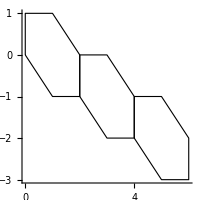

```mathematica
hexagonCell[offset_:{0,0},basis_List:{{Sqrt[3]/2,1/2},{0,1}}]:=Module[
{a=basis[[1]],b=basis[[2]]},
Translate[Polygon[{{0,0},a-b,2*a-b,2*a,a+b,b}],offset]
];
Graphics[{{EdgeForm[Black],FaceForm[White],hexagonCell[{0,0},{{1,0},{0,1}}]},{EdgeForm[Black],FaceForm[White],hexagonCell[{2,-1},{{1,0},{0,1}}]},{EdgeForm[Black],FaceForm[White],hexagonCell[2*{2,-1},{{1,0},{0,1}}]}},ImageSize->200,Axes->True]
```

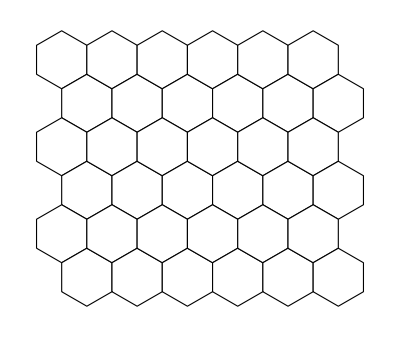

```mathematica
Graphics[Table[{EdgeForm[Black],FaceForm[White],hexagonCell[{i*{Sqrt[3],0}-j*{0,3/2}+If[EvenQ[j],0,1]*{Sqrt[3]/2,0}},{{Sqrt[3]/2,1/2},{0,1}}]},{i,0,5},{j,0,5}]]
```

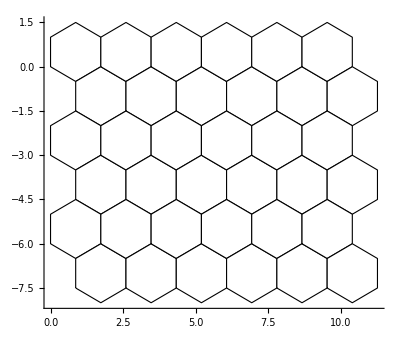

```mathematica
basis={{Sqrt[3]/2,1/2},{0,1}};
Graphics[Table[{EdgeForm[Black],FaceForm[White],hexagonCell[{i*(2*basis[[1]]-basis[[2]])-If[EvenQ[j],3*j/2*{0,basis[[2,2]]},(3*j/2)*{0,basis[[2,2]]}+1/2{0,basis[[2,2]]-2basis[[1,2]]}]+If[EvenQ[j],0,{basis[[1,1]],0}]},basis]},{i,0,5},{j,0,5}],Axes->True] (* This formula works! Now just to simplify and add this to the general function! *)
```

```mathematica
Solve[a*1+b==2&&a*3+b==5,{a,b}]
```

{{a→3/2,b→1/2}}

```mathematica
basis={{Sqrt[3]/2,1/2},{0,1}};
Graphics[Table[{EdgeForm[Black],FaceForm[White],hexagonCell[{i*(2*basis[[1]]-basis[[2]])-j*{0,basis[[1,2]]+basis[[2,2]]}+If[EvenQ[j],0,1]*{basis[[1,1]],0}},basis]},{i,0,5},{j,0,5}],Axes->True]
```

-Graphics-

```mathematica
Export["hex.jpg",hex]
```

```mathematica
Gray
```

GrayLevel[0.5]